### Parameters

```mathematica
<<MaTeX`
```

```mathematica
texStyle={FontFamily->"Times",FontSize->14};
```

```mathematica
mDp=1869.66;
(* mass of D^0 *)
mD0=1864.84;
(* mass of D^(*+) *)
mDps=2010.26;
(* mass of D^(*0) *)
mD0s=2006.85;
(* use binding energy from unitarized Breit Wigner LHCb fit *)
bindingenergy=-0.360;
mT=mDps+mD0+bindingenergy;
(* pion decay constant *)
fπ=130.;
(* axial coupling of HHχPT *)
g=0.54;
(* mass of π^0 *)
mπ0=134.9768;
(* mass of π^+ *)
mπp=139.57039;
```

### Experimental data

```mathematica
(* data courtesy of Mikhail Mikhasenko.  From him: "Please be aware that these are the representation of the binned data, while we do unbinned likelihood fits in our studies. There might be a loss of precision due to binning." 
*)
```

#### raw data

```mathematica
fig4aXaxis={3.72991,3.73041,3.73091,3.73141,3.73191,3.73241,3.73291,3.73341,3.73391,3.73441,3.73491,3.73541,3.73591,3.73641,3.73691,3.73741,3.73791,3.73841,3.73891,3.73941,3.73991,3.74041,3.74091,3.74141,3.74191,3.74241,3.74291,3.74341,3.74391,3.74441,3.74491,3.74541,3.74591,3.74641,3.74691,3.74741,3.74791,3.74841,3.74891,3.74941,3.74991,3.75041,3.75091,3.75141,3.75191,3.75241,3.75291,3.75341,3.75391,3.75441,3.75491,3.75541,3.75591,3.75641,3.75691,3.75741};
fig4aYaxis={91.87349,83.91322,43.65984,32.40545,22.15956,24.21192,22.38146,16.05066,20.61709,17.76958,15.275,6.41135,14.74418,16.74665,17.8299,11.3512,33.12155,18.3281,20.66652,20.65011,15.08982,15.46257,31.60039,22.50674,10.46671,7.849067,9.293681,15.61505,19.17972,5.768346,18.83466,10.71483,22.12074,11.89772,18.42971,13.30208,17.09842,16.30606,24.00543,27.09684,12.30812,27.87209,13.9568,21.87492,34.95869,20.41001,23.9531,19.04171,24.03083,18.4567,15.25985,21.42472,25.46886,18.04251,23.55832,21.16552};
fig4aError={10.9283,10.09399,7.560818,7.044639,5.961235,6.237155,5.864415,5.043657,6.133625,5.610891,5.627861,4.378205,5.827929,5.712013,5.695677,5.36071,6.790226,6.175454,6.298213,5.975063,5.693189,6.22815,7.128134,6.42513,5.541696,5.42431,5.049529,5.836657,6.207817,5.204006,6.31746,5.121723,6.512871,5.813573,6.370801,6.086546,6.390469,5.966866,6.841243,7.072078,6.421888,7.250396,5.791154,6.567666,7.844,7.001333,6.626488,6.174498,6.605388,6.242446,6.41643,6.557458,6.923712,6.096799,7.202532,6.598221};
fig4aBkgrdPoints(*from WebPlotDigitizer*)={{3.7302171428571427,4.752623688155921},{3.7304914285714283,5.689655172413779},{3.7311085714285714,7.751124437781101},{3.7314171428571425,8.500749625187382},{3.732137142857143,10},{3.732445714285714,10.562218890554703},{3.733165714285714,11.686656671664167},{3.733508571428571,12.248875562218899},{3.734262857142857,13.185907046476757},{3.7354285714285713,14.49775112443777},{3.7366971428571425,15.434782608695627},{3.7379314285714282,16.55922038980509},{3.739268571428571,17.496251874062963},{3.7402971428571425,17.87106446776609},{3.741805714285714,18.6206896551724},{3.743245714285714,19.18290854572713},{3.745028571428571,19.557721139430285},{3.746365714285714,19.932533733133425},{3.747702857142857,20.119940029985003},{3.7496571428571426,20.307346326836566},{3.751611428571428,20.307346326836566},{3.7535314285714283,20.307346326836566},{3.755245714285714,20.119940029985003},{3.756788571428571,19.745127436281862}};
fig4a=Table[{1000fig4aXaxis[[i]],Around[fig4aYaxis[[i]]-Interpolation[fig4aBkgrdPoints,fig4aXaxis[[i]]],fig4aError[[i]]]},{i,1,Length[fig4aXaxis]}];
fig4bXaxis={3.73473,3.73523,3.73573,3.73623,3.73673,3.73723,3.73773,3.73823,3.73873,3.73923,3.73973,3.74023,3.74073,3.74123,3.74173,3.74223,3.74273,3.74323,3.74373,3.74423,3.74473,3.74523,3.74573,3.74623,3.74673,3.74723,3.74773,3.74823,3.74873,3.74923,3.74973,3.75023,3.75073,3.75123,3.75173,3.75223,3.75273,3.75323,3.75373,3.75423,3.75473,3.75523,3.75573,3.75623,3.75673,3.75723};
fig4bYaxis={38.04047,36.18541,40.80066,30.92631,14.30568,28.23303,23.64475,19.0599,16.53869,23.00334,17.32386,9.817419,24.99132,19.97771,8.07264,34.64889,23.34397,27.00311,18.80671,18.57994,17.62958,14.99337,11.93305,25.45009,12.78334,16.77578,9.714108,12.36677,12.338,24.68596,7.384336,19.38121,32.93354,19.76261,13.48532,20.70776,15.48021,21.8253,24.46633,20.61676,17.59626,12.46061,17.51616,30.63834,7.505555,19.3337};
fig4bError={7.464232,7.242437,7.460643,6.965002,5.898423,6.267186,6.621599,6.014302,6.137484,6.423124,6.289081,5.65899,6.90446,7.104523,5.728642,7.965738,6.622948,7.251705,5.89567,7.252382,6.872203,6.251087,6.331838,6.776095,6.21899,6.613073,5.826992,6.449921,5.899172,7.436035,6.053245,6.339896,7.859357,6.784779,6.216847,7.007693,6.162625,6.932399,7.224195,7.043905,7.136549,6.878359,6.447563,7.354987,6.327336,7.543988};
fig4bBkgrdPoints(*from WebPlotDigitizer*)={{3.7346105263157896,3.0322580645161423},{3.734778947368421,4.246334310850443},{3.735143859649123,6.404692082111438},{3.7353684210526317,7.348973607038133},{3.7358175438596493,8.967741935483886},{3.7361263157894737,9.777126099706749},{3.7365754385964913,10.991202346041064},{3.7369122807017545,11.665689149560123},{3.7373894736842104,12.609970674486803},{3.7377263157894736,13.149560117302059},{3.73820350877193,13.958944281524921},{3.7385684210526318,14.498533724340191},{3.7390736842105263,15.173020527859236},{3.7394385964912282,15.577712609970689},{3.739943859649123,16.117302052785917},{3.7403087719298247,16.38709677419355},{3.7408140350877193,16.79178885630499},{3.741178947368421,17.196480938416414},{3.7416842105263157,17.46627565982405},{3.742021052631579,17.736070381231684},{3.742554385964912,18.005865102639305},{3.742919298245614,18.27565982404691},{3.7434245614035087,18.41055718475073},{3.7443508771929825,18.815249266862182},{3.7446877192982457,18.950146627565985},{3.7451929824561403,19.085043988269803},{3.745557894736842,19.21994134897362},{3.7460912280701755,19.35483870967741},{3.7464280701754387,19.35483870967741},{3.74698947368421,19.35483870967741},{3.7473263157894734,19.489736070381227},{3.7478596491228067,19.489736070381227},{3.7481684210526316,19.624633431085044},{3.748757894736842,19.489736070381227},{3.749094736842105,19.489736070381227},{3.7496,19.35483870967741},{3.7499649122807015,19.35483870967741},{3.7505263157894735,19.21994134897362},{3.7508631578947367,19.085043988269803},{3.7513684210526312,18.950146627565985},{3.7519298245614032,18.950146627565985},{3.7528842105263154,18.41055718475073},{3.7542035087719294,18.005865102639305},{3.7552982456140347,17.601173020527867},{3.7562245614035086,17.196480938416414},{3.7569263157894732,16.52199413489737}};
fig4b=Table[{1000fig4bXaxis[[i]],Around[fig4bYaxis[[i]]-Interpolation[fig4bBkgrdPoints,fig4bXaxis[[i]]],fig4bError[[i]]]},{i,1,Length[fig4bXaxis]}];
```

InterpolatingFunction::dmval: Input value {3.72991} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.75691} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.75741} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.75723} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
fig4aNoError=Table[{1000fig4aXaxis[[i]],fig4aYaxis[[i]]-Interpolation[fig4aBkgrdPoints,fig4aXaxis[[i]]]},{i,1,Length[fig4aXaxis]}];
fig4bNoError=Table[{1000fig4bXaxis[[i]],fig4bYaxis[[i]]-Interpolation[fig4bBkgrdPoints,fig4bXaxis[[i]]]},{i,1,Length[fig4bXaxis]}];
```

InterpolatingFunction::dmval: Input value {3.72991} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.75691} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.75741} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {3.75723} lies outside the range of data in the interpolating function. Extrapolation will be used.

#### plot

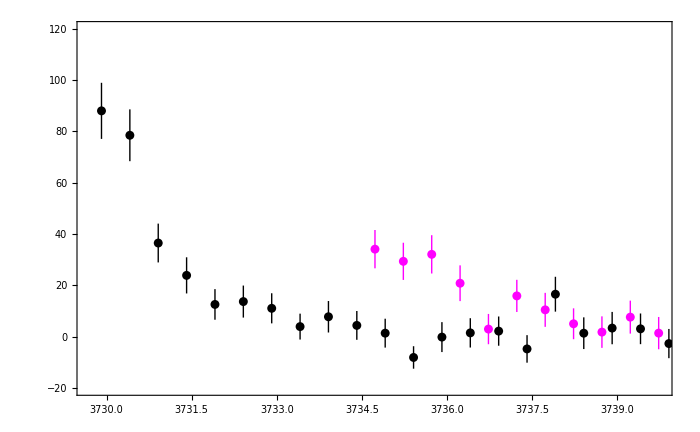

```mathematica
RawDataPlot=ListPlot[{fig4a,fig4b},PlotRange->{{2mD0,mT-mπ0},{-20,120}},PlotStyle->{{Black},{Magenta}},ImageSize->700,FrameStyle->Black,Frame->True,BaseStyle->texStyle,PlotLegends->Placed[{MaTeX["D^0 D^0 \;\\text{final state data}",Magnification->1.5],MaTeX["D^+ D^0 \;\\text{final state data}",Magnification->1.5]},{Right,Top}]]
```

### Least squares fit

```mathematica
With[{ip=Interpolation[LOData1]},LO1[x_/;mD0+mDp<=x<=mT-mπ0]:=ip[x]]
With[{ip=Interpolation[LOData2]},LO2[x_/;2mD0<=x<=mT-mπp]:=ip[x]]
```

```mathematica
Drop[fig4bNoError,-37]
```

{{3734.73,34.1343},{3735.23,29.3943},{3735.73,32.1126},{3736.23,20.8593},{3736.73,2.99148},{3737.23,15.9247},{3737.73,10.489},{3738.23,5.05978},{3738.73,1.81305}}

```mathematica
Fit[Drop[fig4bNoError,-37],{LO1[mDD]},mDD]
```

7.80418×10^7 LO1[mDD]

```mathematica
Drop[fig4aNoError,-47]
```

{{3729.91,88.025},{3730.41,78.5086},{3730.91,36.5218},{3731.41,23.9207},{3731.91,12.6004},{3732.41,13.7123},{3732.91,11.086},{3733.41,3.95962},{3733.91,7.79292}}

```mathematica
Fit[Drop[fig4aNoError,-47],{LO2[mDD]},mDD]
```

6.80135×10^7 LO2[mDD]

### Plots

For the plots where I only plot certain contributions, I would regenerate the data with the appropriate parameters set to zero to get rid of those contributions.

#### All NLO contributions

```mathematica
With[{ip=Interpolation[LOData1]},LO1[x_/;mD0+mDp<=x<=mT-mπ0]:=ip[x]]
With[{ip=Interpolation[LOData2]},LO2[x_/;2mD0<=x<=mT-mπp]:=ip[x]]
With[{ip=Interpolation[MinData1]},Min1[x_/;mD0+mDp<=x<=mT-mπ0]:=ip[x]]
With[{ip=Interpolation[MinData2]},Min2[x_/;2mD0<=x<=mT-mπp]:=ip[x]]
With[{ip=Interpolation[MaxData1]},Max1[x_/;mD0+mDp<=x<=mT-mπ0]:=ip[x]]
With[{ip=Interpolation[MaxData2]},Max2[x_/;2mD0<=x<=mT-mπp]:=ip[x]]
(* set normalization from least squares fit *)
N1=7.804178731515312*^7;
N2=6.801345397923933*^7;
TeXLegend[legend_]:=Placed[MaTeX[legend,Magnification->1.5],{Right,Top}]
(* plot title *)
title=MaTeX["{\\rm All \\; NLO \\; contributions}",Magnification->1.5];
Show[Plot[{Legended[N1 LO1[mDD],TeXLegend["T_{cc}^+ \\rightarrow D^+ D^0 \\pi^0"]],N1 Min1[mDD],N1 Max1[mDD],Legended[N2 LO2[mDD],TeXLegend["T_{cc}^+ \\rightarrow D^0 D^0 \\pi^+"]],N2 Min2[mDD],N2 Max2[mDD]},{mDD,2mD0,mT-mπ0},PlotLabel->title,ImageSize->700,FrameStyle->Black,Frame->True,BaseStyle->texStyle,PlotRange->{0,150},PlotStyle->{{Blue},{Blue,Dashed},{Blue,Dashed},{Red},{Red,Dashed},{Red,Dashed}}],RawDataPlot]
(*Export["AllNLOcontribs.pdf",%];*)
```

-Graphics-

```mathematica
Grid[{{Rotate[MaTeX["d\\Gamma/dm_{DD}",Magnification->1.5],90Degree],%},{"",MaTeX["m_{DD} \\; [\\text{MeV}]",Magnification->1.5]}}]
```

-Graphics- | -Graphics-
 | -Graphics-

#### NA and self energy contributions

```mathematica
With[{ip=Interpolation[LOData1]},LO1[x_/;mD0+mDp<=x<=mT-mπ0]:=ip[x]]
With[{ip=Interpolation[LOData2]},LO2[x_/;2mD0<=x<=mT-mπp]:=ip[x]]
With[{ip=Interpolation[MaxData1]},Max1[x_/;mD0+mDp<=x<=mT-mπ0]:=ip[x]]
With[{ip=Interpolation[MaxData2]},Max2[x_/;2mD0<=x<=mT-mπp]:=ip[x]]
(* set normalization from least squares fit *)
N1=7.804178731515312*^7;
N2=6.801345397923933*^7;
TeXLegend[legend_]:=Placed[MaTeX[legend,Magnification->1.5],{Right,Top}]
(* plot title *)
title=MaTeX["{\\rm Non-analytic \\; and \\; NLO \\; self-energy \\; contributions}",Magnification->1.5];
Show[Plot[{Legended[N1 LO1[mDD],TeXLegend["T_{cc}^+ \\rightarrow D^+ D^0 \\pi^0"]],N1 Max1[mDD],Legended[N2 LO2[mDD],TeXLegend["T_{cc}^+ \\rightarrow D^0 D^0 \\pi^+"]],N2 Max2[mDD]},{mDD,2mD0,mT-mπ0},PlotLabel->title,ImageSize->700,FrameStyle->Black,Frame->True,BaseStyle->texStyle,PlotRange->{0,110},PlotStyle->{{Blue},{Blue,Dashed},{Red},{Red,Dashed}}],RawDataPlot]
```

-Graphics-

```mathematica
Grid[{{Rotate[MaTeX["d\\Gamma/dm_{DD}",Magnification->1.5],90Degree],%},{"",MaTeX["m_{DD} \\; [\\text{MeV}]",Magnification->1.5]}}]
```

-Graphics- | -Graphics-
 | -Graphics-

#### C0D contributions

```mathematica
With[{ip=Interpolation[LOData1]},LO1[x_/;mD0+mDp<=x<=mT-mπ0]:=ip[x]]
With[{ip=Interpolation[LOData2]},LO2[x_/;2mD0<=x<=mT-mπp]:=ip[x]]
With[{ip=Interpolation[MinData1]},Min1fm25[x_/;mD0+mDp<=x<=mT-mπ0]:=ip[x]]
With[{ip=Interpolation[MinData2]},Min2fm25[x_/;2mD0<=x<=mT-mπp]:=ip[x]]
With[{ip=Interpolation[MaxData1]},Max1fm25[x_/;mD0+mDp<=x<=mT-mπ0]:=ip[x]]
With[{ip=Interpolation[MaxData2]},Max2fm25[x_/;2mD0<=x<=mT-mπp]:=ip[x]]
```

```mathematica
With[{ip=Interpolation[MinData1]},Min1fm1[x_/;mD0+mDp<=x<=mT-mπ0]:=ip[x]]
With[{ip=Interpolation[MinData2]},Min2fm1[x_/;2mD0<=x<=mT-mπp]:=ip[x]]
With[{ip=Interpolation[MaxData1]},Max1fm1[x_/;mD0+mDp<=x<=mT-mπ0]:=ip[x]]
With[{ip=Interpolation[MaxData2]},Max2fm1[x_/;2mD0<=x<=mT-mπp]:=ip[x]]
```

```mathematica
(* set normalization from least squares fit *)
N1=7.804178731515312*^7;
N2=6.801345397923933*^7;
TeXLegend[legend_]:=Placed[MaTeX[legend,Magnification->1.5],{Right,Top}]
(* plot title *)
title=MaTeX["{\\rm Contributions \\; from \\;} C_{0D} {\\rm \\; interactions}",Magnification->1.5];
Show[Plot[{Legended[N1 LO1[mDD],TeXLegend["T_{cc}^+ \\rightarrow D^+ D^0 \\pi^0"]],Legended[N1 Min1fm25[mDD],TeXLegend["|C_{0D}|=0.25 \\; {\\rm fm}^2"]],Legended[N1 Min1fm1[mDD],TeXLegend["|C_{0D}|=1 \\; {\\rm fm}^2"]],N1 Max1fm25[mDD],N1 Max1fm1[mDD],Legended[N2 LO2[mDD],TeXLegend["T_{cc}^+ \\rightarrow D^0 D^0 \\pi^+"]],Legended[N2 Min2fm25[mDD],TeXLegend["|C_{0D}|=0.25 \\; {\\rm fm}^2"]],Legended[N2 Min2fm1[mDD],TeXLegend["|C_{0D}|=1 \\; {\\rm fm}^2"]],N2 Max2fm25[mDD],N2 Max2fm1[mDD]},{mDD,2mD0,mT-mπ0},PlotLabel->title,ImageSize->700,FrameStyle->Black,Frame->True,BaseStyle->texStyle,PlotRange->{0,110},PlotStyle->{{Blue},{Blue,Dotted},{Blue,Dashed},{Blue,Dotted},{Blue,Dashed},{Red},{Red,Dotted},{Red,Dashed},{Red,Dotted},{Red,Dashed}}],RawDataPlot]
```

-Graphics-

```mathematica
Grid[{{Rotate[MaTeX["d\\Gamma/dm_{DD}",Magnification->1.5],90Degree],%},{"",MaTeX["m_{DD} \\; [\\text{MeV}]",Magnification->1.5]}}]
```

-Graphics- | -Graphics-
 | -Graphics-

#### β contributions

```mathematica
(* I accidentally left the names on the RHS as min even though they should be Max*)
```

```mathematica
With[{ip=Interpolation[LOData1]},LO1[x_/;mD0+mDp<=x<=mT-mπ0]:=ip[x]]
With[{ip=Interpolation[LOData2]},LO2[x_/;2mD0<=x<=mT-mπp]:=ip[x]]
With[{ip=Interpolation[MaxData1]},Min1β1[x_/;mD0+mDp<=x<=mT-mπ0]:=ip[x]]
With[{ip=Interpolation[MaxData2]},Min2β1[x_/;2mD0<=x<=mT-mπp]:=ip[x]]
```

```mathematica
With[{ip=Interpolation[MaxData1]},Min1β6[x_/;mD0+mDp<=x<=mT-mπ0]:=ip[x]]
With[{ip=Interpolation[MaxData2]},Min2β6[x_/;2mD0<=x<=mT-mπp]:=ip[x]]
```

```mathematica
(* set normalization from least squares fit *)
N1=7.804178731515312*^7;
N2=6.801345397923933*^7;
TeXLegend[legend_]:=Placed[MaTeX[legend,Magnification->1.5],{Right,Top}]
(* plot title *)
title=MaTeX["{\\rm Contributions \\; from \\;} \\beta_2 {\\rm \\; and \\;} \\beta_4",Magnification->1.5];
Show[Plot[{Legended[N1 LO1[mDD],TeXLegend["T_{cc}^+ \\rightarrow D^+ D^0 \\pi^0"]],Legended[N1 Min1β1[mDD],TeXLegend["\\beta_{2/4}=-0.1"]],Legended[N1 Min1β6[mDD],TeXLegend["\\beta_{2/4}=-0.59"]],Legended[N2 LO2[mDD],TeXLegend["T_{cc}^+ \\rightarrow D^0 D^0 \\pi^+"]],Legended[N2 Min2β1[mDD],TeXLegend["\\beta_{2/4}=-0.1"]],Legended[N2 Min2β6[mDD],TeXLegend["\\beta_{2/4}=-0.59"]]},{mDD,2mD0,mT-mπ0},PlotLabel->title,ImageSize->700,FrameStyle->Black,Frame->True,BaseStyle->texStyle,PlotRange->{0,160},PlotStyle->{{Blue},{Blue,Dotted},{Blue,Dashed},{Red},{Red,Dotted},{Red,Dashed}}],RawDataPlot]
```

-Graphics-

```mathematica
Grid[{{Rotate[MaTeX["d\\Gamma/dm_{DD}",Magnification->1.5],90Degree],%},{"",MaTeX["m_{DD} \\; [\\text{MeV}]",Magnification->1.5]}}]
```

-Graphics- | -Graphics-
 | -Graphics-

### Plots with constant propagator

```mathematica
With[{ip=Interpolation[LODataNormalized1]},LONormalized1[x_/;mD0+mDp<=x<=mT-mπ0]:=ip[x]]
With[{ip=Interpolation[LODataConstNormalized1]},LOConstNormalized1[x_/;mD0+mDp<=x<=mT-mπ0]:=ip[x]]
With[{ip=Interpolation[LODataNormalized2]},LONormalized2[x_/;2mD0<=x<=mT-mπp]:=ip[x]]
With[{ip=Interpolation[LODataConstNormalized2]},LOConstNormalized2[x_/;2mD0<=x<=mT-mπp]:=ip[x]]
```

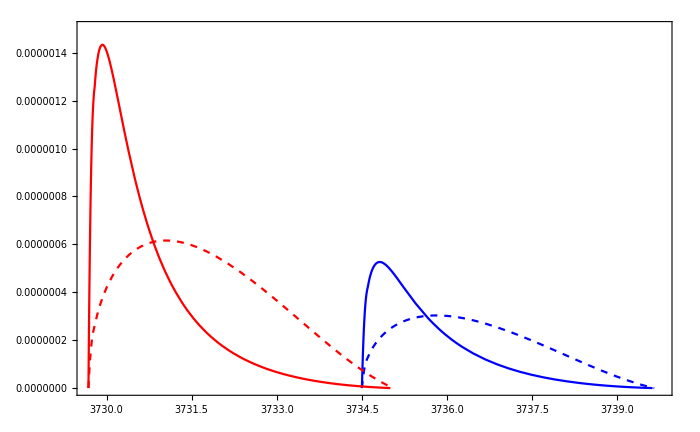

```mathematica
Plot[{Legended[LONormalized1[mDD],Placed[MaTeX["T_{cc}^+ \\rightarrow D^+ D^0 \\pi^0",Magnification->1.5],{Right,Top}]],LOConstNormalized1[mDD],Legended[LONormalized2[mDD],Placed[MaTeX["T_{cc}^+ \\rightarrow D^0 D^0 \\pi^+",Magnification->1.5],{Right,Top}]],LOConstNormalized2[mDD]},{mDD,2mD0,mT-mπ0},ImageSize->700,FrameStyle->Black,Frame->True,BaseStyle->texStyle,PlotStyle->{{Blue},{Blue,Dashed},{Red},{Red,Dashed}},PlotRange->{0,1.5 10^-6}]
```

```mathematica
Grid[{{Rotate[MaTeX["d\\Gamma_{\\rm LO}/dm_{DD}",Magnification->1.5],90Degree],%501},{"",MaTeX["m_{DD} \\; [\\text{MeV}]",Magnification->1.5]}}]
```

-Graphics- | -Graphics-
 | -Graphics-